```mathematica
gap=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gap/GapD.d.0.075.p0.1.v11e4-e5-e6-e3-max.txt",{Number,Number}];
```

```mathematica
d=0.07;
ClearAll[a,b,p,α]
m=11;
pg1[m-1]=α;
pg1[m]=(1-3p-α(1-4p))α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m];
pg1[m+1]=p(1-α)α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m+1];
For [i=m+2,i<501,i++,
pg1[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]
a=0;
α=p/(1/d-m-0.5);
p=0.09;
Solve[Sum[pg1[x],{x,m-1,500}]==1,b]
```

{{b→-7.02963}}

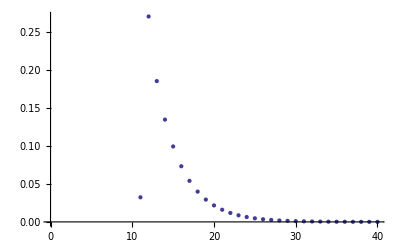

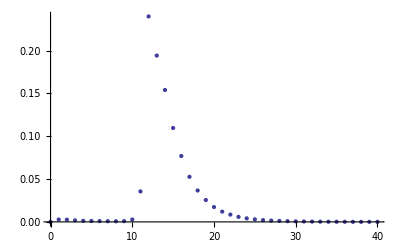

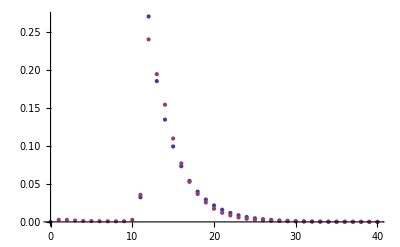

```mathematica
b=-7.029631125585417;
data1=Table[{i+1,pg1[i]},{i,m-1,300}];
ListPlot[{data1},PlotRange->{{0,40},Full}]
ListPlot[{gap},PlotRange->{{0,40},Full}]
ListPlot[{data1,gap},PlotRange->{{0,40},Full}]
```

```mathematica
------------------------------------------------------------------
```

```mathematica
d=0.075;
ClearAll[a,b,p,g,m,α]
m=11;
v1[m-3]=p*p;
v1[m-2]=p*(1-p);
v1[m-1]=1-p;
v[m-2]=p*p;
v[m-1]=p*(1-p);
v[m]=1-p;
v2[m-3]=a*p*p;
v2[m-2]=a*p*(1-p)+(1-a)*p*p;
v2[m-1]=a*(1-p)+(1-a)*p*(1-p);
v2[m]=(1-a)*(1-p);
For [i=m+3,i<1001,i++,
g[i]=Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][i];
]
g[m-1]=α;
a=0;
α=p(1-p)/(1/d-m-0.5);
p=0.1;
g[m+2]=g[m-1]*(v1[m-3]*v2[m])+Function[{u},a-b*Exp[-u/(p*(1-p)/α+0.5)]][m+2];
Solve[{x==g[m-1]*(v1[m-3]*v2[m-2]+v1[m-2]*v2[m-1]+v1[m-1]*v2[m])+x*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+
y*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+2]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+3]*(v[m]*v2[m-3]),y==g[m-1]*(v1[m-3]*v2[m-1]+v1[m-2]*v2[m])+x*(v[m-2]*v2[m-1]+v[m-1]*v2[m])+y*(v[m-2]*v2[m-2]+v[m-1]*v2[m-1]+v[m]*v2[m])+g[m+2]*(v[m-2]*v2[m-3]+v[m-1]*v2[m-2]+v[m]*v2[m-1])+g[m+3]*(v[m-1]*v2[m-3]+v[m]*v2[m-2])+g[m+4]*(v[m]*v2[m-3])},{x,y}]
```

{{x→0.28983-0.00127453 b,y→0.152881-0.00241103 b}}

```mathematica
g[m]=0.28983025400206297-0.0012745253976972927 b;
g[m+1]=0.15288134304953432-0.002411029918458674 b;
Solve[Sum[g[x],{x,m-1,200}]==1,b]
```

{{b→-34.7731}}

```mathematica
b=-34.77305996179277;
data2=Table[{i+1,g[i]},{i,m-1,300}];
```

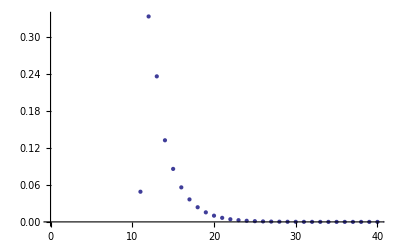

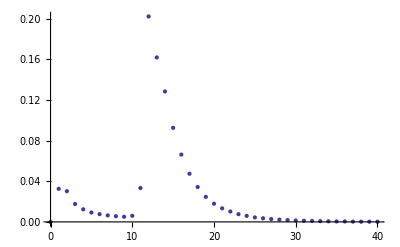

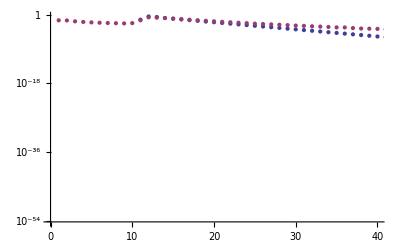

```mathematica
ListPlot[{data2},PlotRange->{{0,40},Full}]
ListPlot[{gap},PlotRange->{{0,40},Full}]
ListLogPlot[{data2,gap},PlotRange->{{0,40},Full}]
```